# Electrochemical Model for Multi Electrode Arrays

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

## Two-dimensional Electrode Array Droplet Network Model

In this section, we extend our formulation to two dimensions. To check the stability, we test our formulation by applying random periodic patterns. In the next version, you will be able to define specific potentials as well as based on feedback loop as required by the algorithm.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

```mathematica
elecRadius=UnitConvert@Quantity[1.0,"mm"] ;(* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1.0,"mm"];(* Gap between two nearby electrodes *)
```

```mathematica
dropHeight=UnitConvert@Quantity[1.0,"mm"]; (* Height of the droplet above electrode array *)
```

```mathematica
Cdl=UnitConvert@Quantity[0.02,"F/m^2"];(* Double Layer capacitance per unit area *)
```

```mathematica
CBack=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[25 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
𝒟=UnitConvert@Quantity[1 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[0.7 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity *)
```

0.751454 per meterper ohm

```mathematica
dropletBulkR1= 1/BulkCond elecGap/dropHeight^2
```

1330.75 Ω

```mathematica
dropletBulkR = 1/BulkCond(2dropHeight)/elecGap^2
```

2661.51 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

0.0000212182 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[FullSimplify[ j0[CEl,CEl,khom]],"A/m^2"]
```

6.03033 A/m^2

```mathematica
ExCurrentDensity/iLim
```

0.892857

#### Governing equations of single droplet (Non Boundary)

Similar to the previous section, the governing equations are implemented for the neighbouring electrodes.

```mathematica
eq1[n_]:=Symbol["i"<>ToString[n]<>"L"][t]+Symbol["i"<>ToString[n]<>"R"][t]==Symbol["iEL"<>ToString[n]][t]
```

```mathematica
eq2[n_]:=Symbol["iEL"<>ToString[n]][t]==D[Evaluate[V-Symbol["ϕ"<>ToString[n]][t]-E0],t]+Evaluate[AreaEL i0 (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)]))/.ηm-> Evaluate[V-Symbol["ϕ"<>ToString[n]][t]-E0]]
```

```mathematica
eq3[n_]:=Symbol["ϕ"<>ToString[n]][t]-Symbol["ϕP"<>ToString[n]][t]==RBulkA Symbol["iEL"<>ToString[n]][t]
```

```mathematica
eq4[n_]:= Symbol["ϕP"<>ToString[n]][t]-Symbol["ϕPL"<>ToString[n]][t]==RBulkB Symbol["i"<>ToString[n]<>"L"][t]
```

```mathematica
eq5[n_]:= Symbol["ϕP"<>ToString[n]][t]-Symbol["ϕPR"<>ToString[n]][t]==RBulkB Symbol["i"<>ToString[n]<>"R"][t]
```

```mathematica
{eq1[n],eq2[n],eq3[n],eq4[n],eq5[n]}//TableForm
```

inL[t]+inR[t]==iELn[t]
iELn[t]==(AreaEL (-ⅇ^(αc (-38.9413 s^3 A/(kg m^2)) (-E0+V-ϕn[t]))+ⅇ^(αa (38.9413 s^3 A/(kg m^2)) (-E0+V-ϕn[t]))) i0)/(1+((ⅇ^(αc (-38.9413 s^3 A/(kg m^2)) (-E0+V-ϕn[t]))+ⅇ^(αa (38.9413 s^3 A/(kg m^2)) (-E0+V-ϕn[t]))) i0)/iL)-ϕn'[t]
ϕn[t]-ϕPn[t]==RBulkA iELn[t]
-ϕPLn[t]+ϕPn[t]==RBulkB inL[t]
ϕPn[t]-ϕPRn[t]==RBulkB inR[t]

These set of equations are valid for a droplet surrounded by neighbouring droplets.

#### With modified Butler-Volmer Kinetics

```mathematica
λ=1 10^-4; (* Defines the sharpness of the rectangular wave *)
```

```mathematica
sqr[k_,x_]:=(2 ArcTan[Sin[2π (k x)]/λ]/π);
```

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
droplet2DBV[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[Symbol["V"<>indexStr]Sin[Symbol["ω"<>indexStr]t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/.ηm-> Evaluate[Symbol["V"<>indexStr]Sin[Symbol["ω"<>indexStr]t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DmBV[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[Symbol["V"<>indexStr]Sin[Symbol["ω"<>indexStr]t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0( (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)])))/.ηm-> Evaluate[Symbol["V"<>indexStr]Sin[Symbol["ω"<>indexStr]t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DsqrBV[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[Symbol["V"<>indexStr]sqr[Symbol["ω"<>indexStr],t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/.ηm-> Evaluate[Symbol["V"<>indexStr]sqr[Symbol["ω"<>indexStr],t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DsqrmBV[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[Symbol["V"<>indexStr]sqr[Symbol["ω"<>indexStr],t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0( (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)])))/.ηm-> Evaluate[Symbol["V"<>indexStr]sqr[Symbol["ω"<>indexStr],t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];
eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕP1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕP"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕP"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPS"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕP"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_]:=Flatten[Table[droplet2DBV[i,j,N],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
nEl=5; (* Number of electrodes *)
```

```mathematica
totTime=15; (* Total time of simulation *)
```

```mathematica
Total@{Length[Flatten@eqns[nEl]⟦All,1⟧],Length[Flatten@eqnsCon[nEl]⟦All,1⟧],Length[dropletEndConnections2D[nEl]⟦1⟧]}
```

335

```mathematica
Total@{Length[Flatten@eqns[nEl]⟦All,2⟧],Length[Flatten@eqnsCon[nEl]⟦All,2⟧],Length[dropletEndConnections2D[nEl]⟦2⟧]}
```

335

```mathematica
{AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,"Cdl"-> Cdl,E0-> 0} (* Parameter List *)
```

{AreaEL→3.14159×10^-6 m^2,RBulk→2661.51 Ω,RBulkA→1330.75 Ω,RBulkB→1330.75 Ω,RConn→2661.51 Ω,i0→6.03033 A/m^2,iL→6.75397 A/m^2,αa→0.5,αc→0.5,Cdl→0.02 s^4 A^2/(kg m^4),E0→0}

```mathematica
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
```

```mathematica
params2=Table[(Symbol["V"<>ToString[i]<>"s"<>ToString[j]]-> RandomReal[{-2,2}]),{i,1,nEl},{j,1,nEl}]//Flatten;
```

```mathematica
params3=Table[(Symbol["ω"<>ToString[i]<>"s"<>ToString[j]]-> RandomInteger[{0,3}]),{i,1,nEl},{j,1,nEl}]//Flatten;
```

```mathematica
eqnsF[N_]:=Flatten[{eqns[N]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}]/.params/.params2/.params3/.q_Quantity:>QuantityMagnitude[q];
```

```mathematica
varsEq[N_]:=Flatten[{eqns[N]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}]
```

```mathematica
ic[N_]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> 0](*,#== 0&/@Evaluate[D[varsEq[5],t]/.t-> 0]*)};
```

```mathematica
eqnsFF=Flatten@{eqnsF[nEl]/.params/.params2/.params3/.q_Quantity:>QuantityMagnitude[q],ic[nEl]};
```

```mathematica
Length/@{Union[eqnsFF],Union[varsEq[nEl]]}
```

{670,335}

```mathematica
Monitor[soln=NDSolve[eqnsFF,varsEq[nEl],{t,0,totTime},MaxSteps->∞,MaxStepSize->0.01,EvaluationMonitor:>(step=t)],step];
```

```mathematica
state[k_]:=ColorData[{"WatermelonColors",{-0.3 10^-3,0.3 10^-3}}][k]
```

```mathematica
state2[k_]:=ColorData[{"TemperatureMap",{-0.2 10^-3,0.2 10^-3}}][k]
```

```mathematica
plotCurrent[t_]=Block[{current},current=Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t])/.First@soln,{i,nEl},{j,nEl}];
Graphics[Flatten@Table[{state[current⟦i,j⟧],Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None]];
```

```mathematica
dataPlot[t_]=Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.soln,{i,nEl},{j,nEl}],2];
```

Plotting all the current at the boundaries along west and south only along first row and column direction.

```mathematica
dataPlot2[t_]= Flatten[Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.soln,{j,nEl}],1];
```

```mathematica
dataPlot3[t_]= Flatten[Table[{j,1,Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]}/.soln,{j,nEl}],1];
```

```mathematica
plotCurrentCon[t_]=Graphics[Table[{state2[dataPlot[t]⟦i,3⟧],Rectangle[{1+2dataPlot[t]⟦i,1⟧-0.45,2dataPlot[t]⟦i,2⟧-0.45},{1+2dataPlot[t]⟦i,1⟧+0.45,2dataPlot[t]⟦i,2⟧+0.45}],state2[dataPlot[t]⟦i,4⟧],Rectangle[{2dataPlot[t]⟦i,1⟧-0.45,1+2dataPlot[t]⟦i,2⟧-0.45},{2dataPlot[t]⟦i,1⟧+0.45,1+2dataPlot[t]⟦i,2⟧+0.45}]},{i,1,nEl^2}]];
```

```mathematica
plotCurrentCon2[t_]=Graphics[Table[{state2[dataPlot2[t]⟦i,3⟧],Rectangle[{2dataPlot2[t]⟦i,1⟧-0.45-1,2dataPlot2[t]⟦i,2⟧-0.45},{2dataPlot2[t]⟦i,1⟧+0.45-1,2dataPlot2[t]⟦i,2⟧+0.45}]},{i,1,nEl}]];
```

```mathematica
plotCurrentCon3[t_]=Graphics[Table[{state2[dataPlot3[t]⟦i,3⟧],Rectangle[{1+2dataPlot3[t]⟦i,1⟧-0.45-1,2dataPlot3[t]⟦i,2⟧-0.45-1},{1+2dataPlot3[t]⟦i,1⟧+0.45-1,2dataPlot3[t]⟦i,2⟧+0.45-1}]},{i,1,nEl}]];
```

```mathematica
Show[{plotCurrentCon2[12],plotCurrentCon3[12],plotCurrentCon[12],plotCurrent[12]}];
```

```mathematica
ListAnimate[Table[plotCurrent[t],{t,0,totTime,0.05}],AnimationRunning-> False]; (* Remove the semicolon to watch the animation *)
```

```mathematica
ListAnimate[Table[plotCurrentCon[t],{t,0,totTime,0.05}],AnimationRunning-> False]; (* Remove the semicolon to watch the animation *)
```

```mathematica
ListAnimate[Monitor[Table[Show[{plotCurrentCon2[t],plotCurrentCon3[t],plotCurrentCon[t],plotCurrent[t]}],{t,0,totTime,0.1}],t],AnimationRunning-> False]
```

## Time dependent Current Patterns on the two dimensional electrode array

```mathematica
ClearAll["Global`*"]
```

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]];(* Vacuum Permittivity *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

```mathematica
elecRadius=UnitConvert@Quantity[1.0,"mm"]; (* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1.0,"mm"];(* Gap between two nearby electrodes *)
```

```mathematica
dropHeight=UnitConvert@Quantity[1.0,"mm"]; (* Height of the droplet above electrode array *)
```

```mathematica
Cdl=UnitConvert@Quantity[0.02,"F/m^2"];(* Double Layer capacitance per unit area *)
```

```mathematica
CBack=UnitConvert@Quantity[300 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
𝒟=UnitConvert@Quantity[1 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[0.7 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity *)
```

2.25436 per meterper ohm

```mathematica
dropletBulkR1= 1/BulkCond elecGap/dropHeight^2
```

443.585 Ω

```mathematica
dropletBulkR = 1/BulkCond(2dropHeight)/elecGap^2
```

887.169 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

0.0000636547 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[ FullSimplify[j0[CEl,CEl,khom]],"A/m^2"]
```

24.1213 A/m^2

```mathematica
ExCurrentDensity/iLim
```

1.19048

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
λ=1 10^-5; (* Defines the sharpness of the rectangular wave *)
```

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ])
```

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DmBV[i_,j_,K_,t0_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{0.01,t0},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0( (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)])))/.ηm-> Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{0.01,t0},t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];
eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕP1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕP"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕP"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕP"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
λ=1 10^-4;
```

```mathematica
nEl=10;  (* Number of electrodes along X/Y *)
```

```mathematica
eqLen1=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,1⟧],Length[Union@dropletEndConnections2D[nEl]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,2⟧],Length[Union@dropletEndConnections2D[nEl]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2]
```

True

No. of variables 1320

```mathematica
{AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}
```

{AreaEL→3.14159×10^-6 m^2,RBulk→887.169 Ω,RBulkA→443.585 Ω,RBulkB→443.585 Ω,RConn→887.169 Ω,i0→24.1213 A/m^2,iL→20.2619 A/m^2,αa→0.5,αc→0.5,0.02 s^4 A^2/(kg m^4)→0.02,E0→0}

```mathematica
params={AreaEL->UnitConvert[ π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;(* Counter for electrode switching operations *)
tS=10; (* Time step for electrode switching *)
offSet=1.0; (* Offset time for setting up/down potential *)
Vapp={}; (* For saving applied electrode potentials *)
```

Testing first step of electrochemical automata (applying potential from 0.0 → 0.25 on all the electrodes)

```mathematica
Clear[soln0,soln1]
```

```mathematica
(* Setting up initial parameters *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,nEl},{j,1,nEl}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]-> 0.25),{i,1,nEl},{j,1,nEl}]//Flatten ;
(* Setting up equations *)
eqnsF[nEl_]:=Flatten[{eqns[nEl,offSet]⟦All,1⟧,eqnsCon[nEl]⟦All,1⟧,eqnsEndCon[nEl]⟦1⟧}];
varsEq[nEl_]:=Flatten[{eqns[nEl,offSet]⟦All,2⟧,eqnsCon[nEl]⟦All,2⟧,eqnsEndCon[nEl]⟦2⟧}];
ic[nEl_]:=Flatten@{#== 0&/@Evaluate[varsEq[nEl]/.t-> 0]};
eqnsFF=Flatten@{eqnsF[nEl]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[nEl]};
Monitor[Evaluate[Symbol["soln"<>ToString[cnTs]]]=NDSolve[eqnsFF,varsEq[nEl],{t,0,tS},MaxSteps->∞,MaxStepSize->0.1,EvaluationMonitor:>(step=t)],step];
```

```mathematica
Vapp=Join[Vapp,{params2i⟦All,2⟧,params2f⟦All,2⟧}];
```

```mathematica
(* Updating parameters for applied electrode potentials *)
params2iN=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,nEl},{j,1,nEl}]],Table[fVShift[{params2i⟦All,2⟧⟦i⟧,params2f⟦All,2⟧⟦i⟧},{λ,offSet},tS],{i,1,nEl^2}]}]; 
params2fN=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]-> RandomReal[{-2.5,2.5}]),{i,1,nEl},{j,1,nEl}]//Flatten ;
(* Setting up equations *)
eqnsF[nEl_]:=Flatten[{eqns[nEl,tS+offSet]⟦All,1⟧,eqnsCon[nEl]⟦All,1⟧,eqnsEndCon[nEl]⟦1⟧}];
varsEq[nEl_]:=Flatten[{eqns[nEl,tS+offSet]⟦All,2⟧,eqnsCon[nEl]⟦All,2⟧,eqnsEndCon[nEl]⟦2⟧}];
ic[nEl_]:=MapThread[{#1==#2}&,{Evaluate[varsEq[nEl]/.t-> tS],First@Evaluate[Evaluate[varsEq[nEl]/.soln0]/.t->tS]}]; 
eqnsFF=Flatten@{eqnsF[nEl]/.params/.params2iN/.params2fN/.q_Quantity:>QuantityMagnitude[q],ic[nEl]};
```

```mathematica
Monitor[Evaluate[Symbol["soln"<>ToString[cnTs+1]]]=NDSolve[eqnsFF,varsEq[nEl],{t,tS,2tS},MaxSteps->10^6,MaxStepSize->0.1,EvaluationMonitor:>(step=t)],step];
```

```mathematica
GraphicsGrid[Partition[Table[Show[{Plot[fVShift[{params2i⟦All,2⟧⟦i⟧,params2f⟦All,2⟧⟦i⟧},{λ,offSet},t],{t,0,tS},PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}],Plot[fVShift[{params2iN⟦All,2⟧⟦i⟧,params2fN⟦All,2⟧⟦i⟧},{λ,tS+offSet},t],{t,tS,2tS},PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]}]},PlotRange-> {{0,2tS},All}],{i,1,nEl^2}],nEl],Frame-> All,ImageSize->1000]; (* Remove the semicolon to view all the potential patterns applied *)
```

Based on the description above, we create an automated code for switching potentials over the electrode array... Note that the electrode potential rises from 0 currently at each electrode switching step.

```mathematica
Clear[λ,tS]
```

```mathematica
offSet=0.5;λ=10^-4;vInit=0.25; (* Initial potential at time step 1*)
```

```mathematica
tS=2.5; (* Time stepping for changing electrochemical potential *)
```

```mathematica
electroChemAutomata[N_,time_,nTs_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
(* 
	N     : Number of electrodes in XY grid 
  time  : Total experimental time  
  nTS   : Total number of electrode switching time steps
Vinit : Bias potential on the electrodes at first time step.
*)
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;
Vapp={}; (* Keeping Applied Potentials *)
solnS={}; (* Keeping Solutions for variables *)
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
(* Updating electrode potentials *)
(* -> For the first step *)
If[cnTs==0,
(* -> Applying initial bias potential *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

(* -> For the generalized step *)
(*params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;*)
params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->RandomReal[{-2.5,2.5}]),{i,1,N},{j,1,N}]//Flatten; 
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
(* -> Applying initial conditions for t=0 *)
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
(* -> Applying initial conditions from previous switching step *)
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
(*Print[eqnsFF]//TableForm;*)
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];
cnTs=cnTs+1;]
];
```

```mathematica
nEl=6; (* Number of electrodes along X and Y *)
```

```mathematica
totalTime = 50; (* Total time of simulation, not important *)
```

```mathematica
numSteps = 15; (* Total number of time steps *)
```

```mathematica
electroChemAutomata[nEl,totalTime,numSteps] (* Running Simulation *)
```

True

No. of variables 480

Current Switching Step: 0

Current Switching Step: 1

Current Switching Step: 2

Current Switching Step: 3

Current Switching Step: 4

Current Switching Step: 5

Current Switching Step: 6

Current Switching Step: 7

Current Switching Step: 8

Current Switching Step: 9

Current Switching Step: 10

Current Switching Step: 11

Current Switching Step: 12

Current Switching Step: 13

Current Switching Step: 14

Current Switching Step: 15

Plotting : Applied potential, current at the electrode and the interface

```mathematica
{Dimensions[Vapp],Dimensions[solnS]}
```

{{16,2,36},{16,480}}

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-2.5,2.5}}][k]; (* Applied Potential *)
state[k_]:=ColorData[{"TemperatureMap",{-0.5 10^-3,0.5 10^-3}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"MintColors",{0,0.5 10^-3}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"GrayYellowTones",{0,1 10^3}}][k]; (* Electric Field Profile *)
```

```mathematica
BL1=BarLegend[{"TemperatureMap",{-2.5,2.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},LegendLabel-> "Applied Voltage (V)",LegendLayout->"Row"];
```

```mathematica
BL2=BarLegend[{"TemperatureMap",{-0.5,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},LegendLabel-> "Electrode Current(mA)",LegendLayout->"Row"];
```

```mathematica
BL3=BarLegend[{"MintColors",{0,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row"];
```

```mathematica
BL4=BarLegend[{"GrayYellowTones",{0,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},LegendLabel-> "Electric Field (10^3 V/m)",LegendLayout->"Row"];
```

```mathematica
{BL1,BL2,BL3,BL4}//TableForm;
```

```mathematica
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl];
Graphics[Flatten@Table[{stateV[plotV⟦i,j⟧],Disk[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->260,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Applied Potential",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC;
Graphics[Flatten@Table[{state[currentEL⟦i,j⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentCon[nEl_,tC_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t] }/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten[{Table[{state2[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state2[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{state2[Abs[dataPlot2⟦i,3⟧]],Rectangle[{2dataPlot2⟦i,1⟧-0.45-1,2dataPlot2⟦i,2⟧-0.45},{2dataPlot2⟦i,1⟧+0.45-1,2dataPlot2⟦i,2⟧+0.45}]},{i,1,nEl}],Table[{state2[Abs[dataPlot3⟦i,3⟧]],Rectangle[{1+2dataPlot3⟦i,1⟧-0.45-1,2dataPlot3⟦i,2⟧-0.45-1},{1+2dataPlot3⟦i,1⟧+0.45-1,2dataPlot3⟦i,2⟧+0.45-1}]},{i,1,nEl}]}],PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentVec[nEl_,tC_,color_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t]}/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten@{color,If[dataPlot⟦#,3⟧≥0,Arrow[{{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧}}],Arrow[{{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧}}]]&/@Range[nEl^2],
If[dataPlot⟦#,4⟧≥0,Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45}}],Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45}}]]&/@Range[nEl^2],
If[dataPlot2⟦#,3⟧≥0,Arrow[{{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧}}],Arrow[{{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧}}]]&/@Range[nEl],
If[dataPlot3⟦#,3⟧≥0,Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1}}],Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1}}]]&/@Range[nEl]
}]];
```

```mathematica
plotEFieldVec[nEl_,tC_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3,AreaF,connectArea,σ},
AreaF=0.3; (* Area Factor to consider the effect of interface *)
connectArea=AreaF QuantityMagnitude@UnitConvert[dropHeight^2,"m^2"];
σ=QuantityMagnitude@BulkCond;
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,1/σ 1/connectArea Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],1/σ 1/connectArea Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,1/σ 1/connectArea Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,1/σ 1/connectArea Symbol["iCS"<>ToString[i]<>"s"<>"1"][t] }/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten@{Table[{state3[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state3[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{Black,Circle[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],Table[{state3[Abs[dataPlot2⟦i,3⟧]],Rectangle[{2dataPlot2⟦i,1⟧-0.45-1,2dataPlot2⟦i,2⟧-0.45},{2dataPlot2⟦i,1⟧+0.45-1,2dataPlot2⟦i,2⟧+0.45}]},{i,1,nEl}],Table[{state3[Abs[dataPlot3⟦i,3⟧]],Rectangle[{1+2dataPlot3⟦i,1⟧-0.45-1,2dataPlot3⟦i,2⟧-0.45-1},{1+2dataPlot3⟦i,1⟧+0.45-1,2dataPlot3⟦i,2⟧+0.45-1}]},{i,1,nEl}]},FrameTicks-> None,Frame-> True,PlotLabel->Text[Style["Electric Field Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plot[nEl_,t_]:=GraphicsRow[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],Show[{plotEFieldVec[nEl,t],plotCurrentVec[nEl,t,Orange]}]},Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]],ImageSize->700]
```

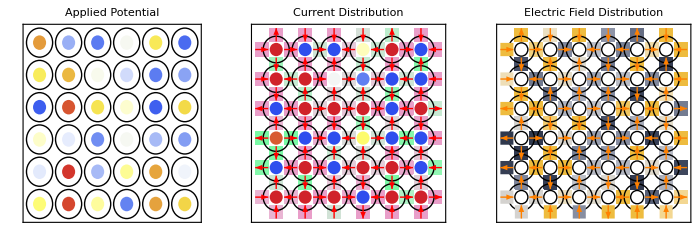

```mathematica
plot[nEl,12]
```

```mathematica
{BL1,BL2,BL3,BL4}//TableForm
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_1.png",plot[nEl,10],ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\ElectrodeArray_CV_1.png

```mathematica
data=Table[plot[nEl,k],{k,0.1,10,0.1}];
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_1.gif",data,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\ElectrodeArray_CV_1.gif

```mathematica
Clear[data];
```

In this section, we create electrode logic operations without the feedback from the chemical information processing.

```mathematica
Clear[λ,tS]
```

```mathematica
offSet=0.5;λ=10^-6;vInit=0.0;tS=2.5; (* Initial potential at time step 1 *)
```

```mathematica
electroChemAutomata[N_,time_,nTs_,potPatterns_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> π elecRadius^2,RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;Vapp={}; solnS={}; 
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
If[cnTs==0,
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];cnTs=cnTs+1;]];
```

```mathematica
plot[nEl_,t_]:=GraphicsRow[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],Show[{plotEFieldVec[nEl,t],plotCurrentVec[nEl,t,Red]}]},Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]]]
```

```mathematica
vInit=0;
```

```mathematica
nEl=7; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=-2.5;
potPatterns//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2.5 | 0 | 0 | 0
0 | 0 | -2.5 | 2.5 | -2.5 | 0 | 0
0 | 0 | 0 | -2.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
electroChemAutomata[nEl,10,1,potPatterns]
```

True

No. of variables 651

Current Switching Step: 0

Current Switching Step: 1

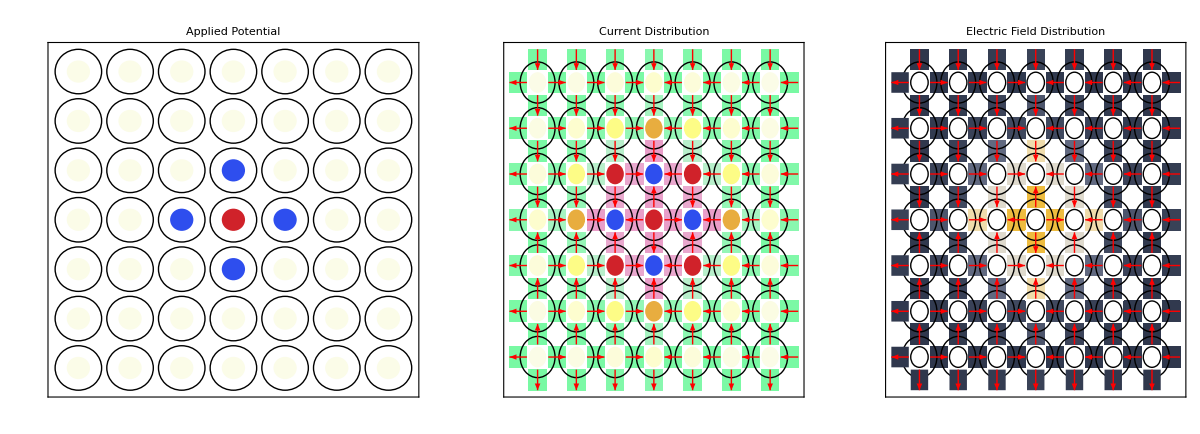

```mathematica
plot[nEl,4]
```

```mathematica
{BL1,BL2,BL3,BL4}//TableForm
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_2.png",plot[nEl,4],ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\ElectrodeArray_CV_2.png

```mathematica
nEl=7; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=2.5;
potPatterns//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.5 | 0 | 0 | 0
0 | 0 | 2.5 | -2.5 | 2.5 | 0 | 0
0 | 0 | 0 | 2.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
electroChemAutomata[nEl,10,1,potPatterns]
```

True

No. of variables 651

Current Switching Step: 0

Current Switching Step: 1

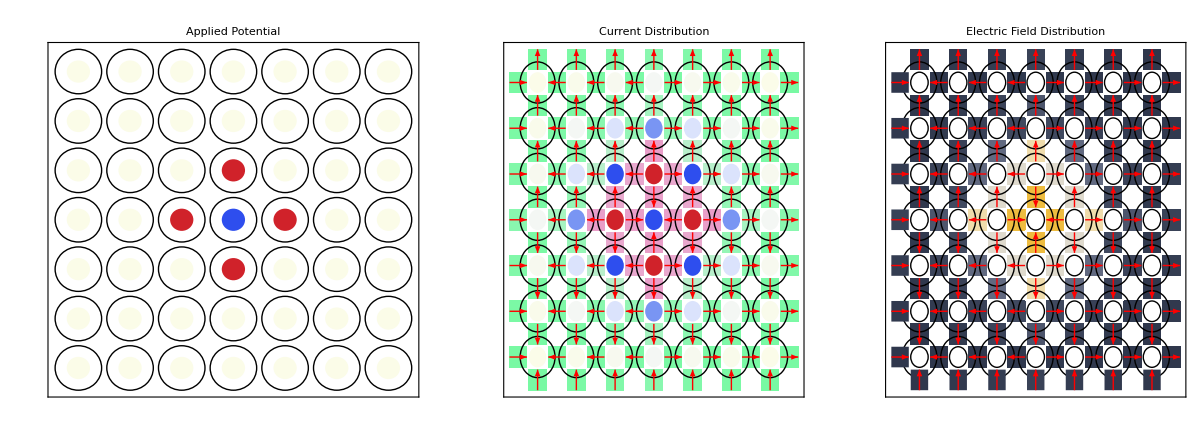

```mathematica
plot[nEl,4]
```

```mathematica
{BL1,BL2,BL3,BL4}//TableForm
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_3.png",plot[nEl,4],ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\ElectrodeArray_CV_3.png